# Data Resolution Mapping

BX Pan
2017.9.18

Cutting

```mathematica
S2SGridSelect[polygon_,cpcdirectory_,s2sdirectory_]:=Block[
{cpcprecip,cpclat,cpclon,s2sprecip,s2slat,s2slon,points,indexes},
	{cpcprecip,cpclat,cpclon}=Map[Import[cpcdirectory,{"Datasets",#}]&,{"precip","lat","lon"}];
	{s2sprecip,s2slat,s2slon}=Map[Import[s2sdirectory,{"Datasets",#}]&,{"tp","latitude","longitude"}];
    cpcprecip=Block[{DownScale,size},
        DownScale[data_,ratio_]:=Block[{convoluter},
			(* This Function performs spacial average downscaling of 2D data through uniform convolution ratio is kind like {5,4}*) 
			convoluter = Block[{net},
   			net = NetInitialize[ConvolutionLayer[1, ratio, "Stride" -> ratio, 
   						"Input" -> Flatten[{1, Dimensions[data]}]]];
               NetReplacePart[net, {"Weights" -> ConstantArray[1./(ratio/.List->Times), Flatten[{1, 1, ratio}]]}]];
            (convoluter@{data})[[1]]];
        size={Round[Abs[s2slat[[2]]-s2slat[[1]]]/Abs[cpclat[[2]]-cpclat[[1]]]],
          Round[Abs[s2slon[[2]]-s2slon[[1]]]/Abs[cpclon[[2]]-cpclon[[1]]]]};
        Map[DownScale[#,size]&,cpcprecip]];
    points=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,points]];
    cpcprecip=Map[cpcprecip[[;;,#[[1]],#[[2]]]]&,indexes];
    s2sprecip=Map[s2sprecip[[;;,;;,#[[1]],#[[2]]]]&,indexes];
    {cpcprecip,s2sprecip}]
```

```mathematica
polygon=westconus[[1]];
cpcdirectory="/Users/lambda/Documents/Data/CPC_Precipitation/global/precip.1982.nc";
s2sdirectory="/Users/lambda/Documents/Data/S2S/BoM/BoM_1982-01-01.nc";
```

```mathematica
{cpcprecip,s2sprecip}=S2SGridSelect[polygon,cpcdirectory,s2sdirectory];
```

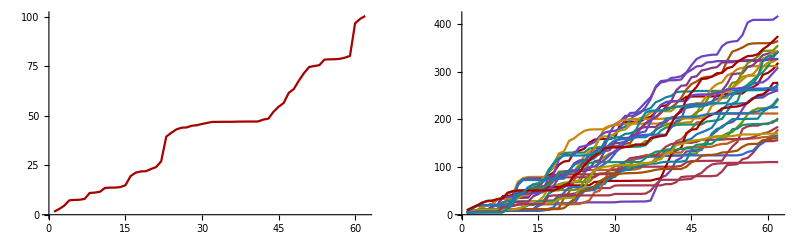
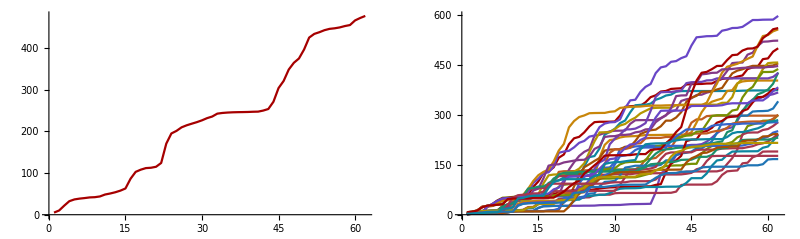
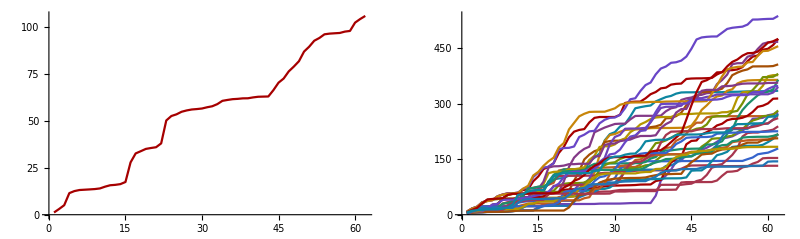
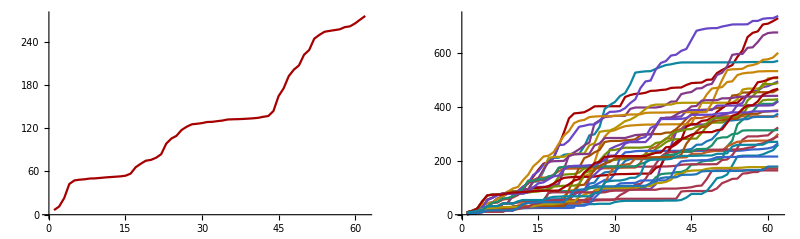
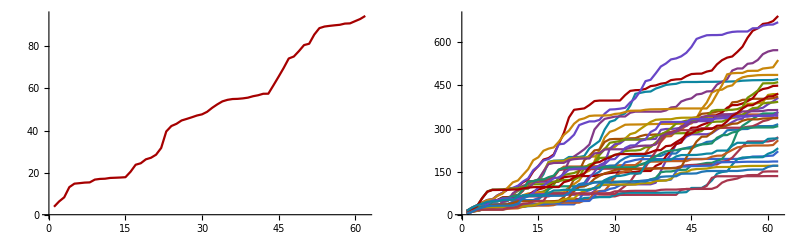
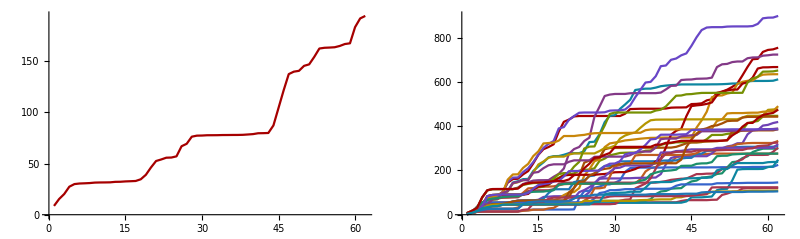
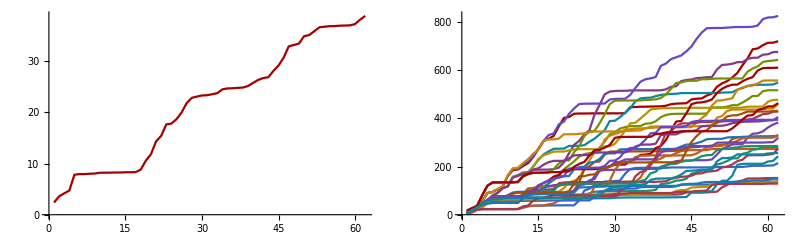
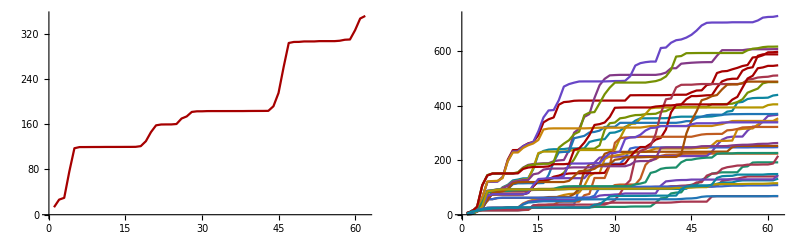

```mathematica
Table[
GraphicsRow[{Block[{cpc=Block[{origin=cpcprecip[[grid,1;;62]]},
				Table[Total[origin[[1;;i]]],{i,1,Length[origin]}]]},
			ListLinePlot[cpc]],
			ListLinePlot[Table[s2sprecip[[grid,;;,i]]*0.04031842735720934+1321.0735907863213,{i,32}]]},
			ImageSize->800],{grid,13}]
```